```mathematica
pdf[x_]:=PDF[ NormalDistribution[0,1],x]
cdf[x_]:=CDF[ NormalDistribution[0,1],x]
prob0[x_,d_,n_]:=1-Exp[-(n-1)*(cdf[x+d]-cdf[x-d])]
prob[d_,n_]:=1-(NIntegrate[pdf[x]*prob0[x,d,n],{x,-∞,∞}])^(n)
```

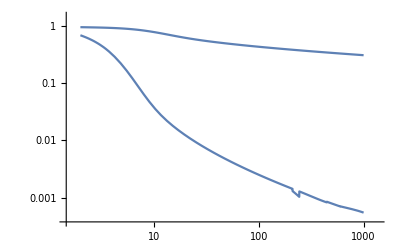

```mathematica
LogLogPlot[Table[1-(NIntegrate[pdf[x]*prob0[x,d,n],{x,-∞,∞}])^(n),{d,{.5,2}}],{n,2,10^3}]
```

```mathematica
prob[.5,2000]
```

0.28052

```mathematica
prob[2,2000]
```

0.000299539

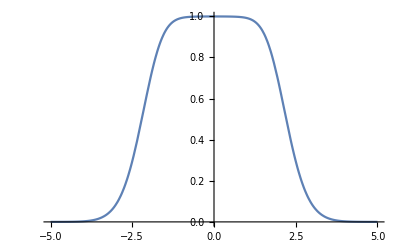

```mathematica
Plot[prob0[x,.01,1000],{x,-5,5}]
```

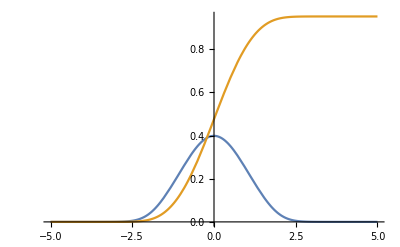

```mathematica
Plot[{pdf[x]*prob0[x,.01,1000],NIntegrate[pdf[z]*prob0[z,.01,1000],{z,-∞,x}]},{x,-5,5}]
```

```mathematica
(1-Erf[.3/2])^10
```

0.158948